```mathematica
ClearAll["Global`*"];
```

```mathematica
Nmax = 15;
Nexp=40;
```

```mathematica
SetPrecision[rp=1,120]
SetPrecision[L=0.1,120]
SetPrecision[l=0,120]
SetPrecision[η=0,120]
SetPrecision[m=0,120]
SetPrecision[ξ=0,120]
nover =1
scalar=0
M1=M/.Solve[-M+rp^2/L^2==0,M][[1]]
```

1.

0.1000000000000000055511151231257827021181583404541015625

0

0

0

«1 more identical outputs»

1

0

100.

```mathematica
F=Simplify[-N[M1]+r^2/L^2];
H=Simplify[1/F];
V=3r^2/(4L^4)-N[M1]/(2L^2)-N[M1]^2/(4r^2)+l^2(1/L^2-N[M1]/r^2)
```

-5000.+7500./x^2-2500. x^2

```mathematica
Plot[V,{r,rp,10}]
```

-Graphics-

```mathematica
r=1/x
```

1/x

```mathematica
A1=Simplify[F];
B1=Simplify[H];
V1= Simplify[V];
DDV=D[V1,x];
xp=1/rp;
```

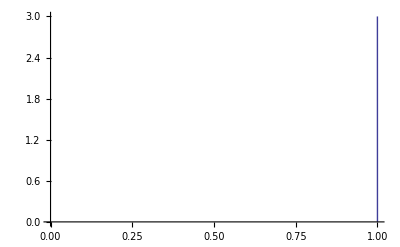

```mathematica
Plot[V1,{x,0,xp},PlotPoints-> {20000},PlotRange-> {0,3}]
```

```mathematica
xp=1/rp
```

1

```mathematica
SQRTAB=Simplify[F]
```

-100.+100./x^2

```mathematica
S[x_]=Chop[ SetPrecision[-1/(x-xp)Simplify[x^4 SQRTAB],120]]
T[x_]=Chop[SetPrecision[-Simplify[(2x^3 SQRTAB+x^4  D[SQRTAB,x]+2I w x^2)],160]];
U[x_]=Chop[SetPrecision[(x-xp)Simplify[(1/SQRTAB  V1 )],120]];
```

-(1. x^2 (99.9999999999999857891452847979962825775146484375-99.9999999999999857891452847979962825775146484375 x^2))/(-1.+x)

```mathematica
S1[x_]=Chop[SetPrecision[Normal[Series[S[x],{x,xp,Nmax}]],120]];
T1[x_]=Chop[SetPrecision[Normal[Series[T[x],{x,xp,Nmax}]],120]];
U1[x_]= Chop[SetPrecision[Normal[Series[U[x],{x,xp,Nmax}]],120]];
```

```mathematica
s=Chop[Simplify[(Table[1/(i!) D[S1[x],{x,i}],{i,0,Nmax}])/.x->xp]];
t=Simplify[(Table[1/(i!) D[T1[x],{x,i}],{i,0,Nmax}])/.x->xp];
u=Simplify[(Table[1/(i!) D[U1[x],{x,i}],{i,0,Nmax}])/.x->xp];
```

```mathematica
DENOMINADOR=SetPrecision[Table[Simplify[i*(i-1)*s[[1]] + i*t[[1]]],{i,1,Nmax}],220];
```

```mathematica
an={1};
Do[
aproximo = Sum[
                 (  (j-1)*(j-2)*s[[i-j+2]] + (j-1)*t[[i-j+2]] + u[[i-j+2]]  )*an[[j]]
                     ,{j,1,i}];
  an=Append[an,Together[aproximo/(-DENOMINADOR[[i]])]]
,{i,1,Nmax}]
```

```mathematica
wfund[NSoma_]:= 
Module[{zeromaquina,psi, poly, modos0,modos1,modos2},

psi[w_]=Together[Sum[an[[i]]*(-xp)^i,{i,1, NSoma}]];
poly=Numerator[psi[w]];

modos0= w/.SetPrecision[NSolve[poly==0,{w}],120];

zeromaquina = 10^(-25);
cond1[x_/;Re[x]<=zeromaquina]:=True;
modos1=Select[modos0,cond1];
modos2=Sort[modos1,Im[#1]>Im[#2]&];
{NSoma,modos2}
]
```

```mathematica
TabelaIm = {};
TabelaRe = {};

Do[
wcalculado =  wfund[i];
TabelaIm = Append[TabelaIm,{wcalculado[[1]],Im[wcalculado[[2]][[nover]]]} ];
TabelaRe = Append[TabelaRe,{wcalculado[[1]],Re[wcalculado[[2]][[nover]]]} ];
,{i,4,Nmax}
  ]//Timing
```

{0.406,Null}

```mathematica
TabelaRe[[Nmax-3]][[2]] + I TabelaIm[[Nmax-3]][[2]]
```

-199.999999999999709227403678601639707190201131059992345486503647640981659050758241758097403383899504418688120586551523472 ⅈ

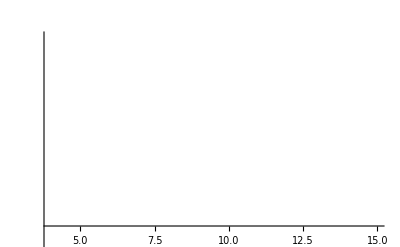

```mathematica
grafIm=ListPlot[TabelaIm,PlotStyle->PointSize[0.02]]
```

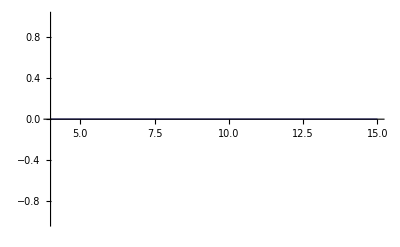

```mathematica
grafRe=ListPlot[TabelaRe,PlotStyle->PointSize[0.02],Joined->True]
```